```mathematica
Du=D[r^2 D[u[r],r],r]+((λ r^2)/v[r]^2-(l(l+1)-(r^2(ω+4π G))/v[r]^2)u[r]);
```

```mathematica
v[r_]:=a^2-b^2 r^2
```

```mathematica
b=0;
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,FullSimplify[Simplify[ExpandAll[Simplify[DSolve[Du==0,u[r],r]]]]]]
```

{{u[r]→1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(C[1]+2^(-2+l) a^(-4+2 l) l √π r^2 λ (-ⅈ r √(-4 G π-ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,-(ⅈ r √(-4 G π-ω))/a^2]+C[2] SphericalBesselY[l,-(ⅈ r √(-4 G π-ω))/a^2]}}

```mathematica
Clear[a,λ,l,G,ω,A,B,b]
```

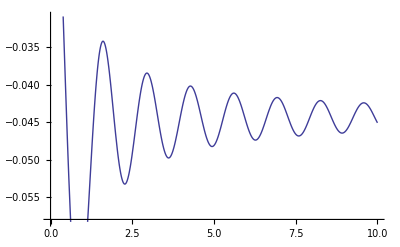

```mathematica
a=1;
λ=1;
l=1;
G=1;
ω=10;
A=0;
B=0;
Plot[{Re[1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]]},{r,0,10}]
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,FullSimplify[1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]]]
```

```mathematica
u[r_,λ_,l_,m_,ω_]:=1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]
```

```mathematica
PreG[r_,rp_,θ_,θp_,ϕ_,ϕp_,t_,tp_]:=-1/(λ+l(l+1)+ω^2-I ϵ)u[r,λ,l,m,ω]u[rp,λ,l,m,ω]SphericalHarmonicY[l,m,θ,ϕ](-1)^m SphericalHarmonicY[l,-m,θp,ϕp]Exp[-I ω(t-tp)]
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,Simplify[PreG[r,rp,θ,θp,ϕ,ϕp,t,tp]]]
```

(-1)^m ⅇ^(-ⅈ (t-tp) ω) (1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]) (1/(4 a^4)π rp^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(rp^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(rp^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π rp^2 λ (rp √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(rp^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(rp √(4 G π+ω))/a^2]) SphericalHarmonicY[l,-m,θp,ϕp] SphericalHarmonicY[l,m,θ,ϕ]

```mathematica
Sum[Sum[PreG[r,rp,θ,θp,ϕ,ϕp,t,tp],{m,-l,l}],{l,0,Infinity}]
```

∑_(l=0)^∞ (∑_(m=-l)^l (-1)^m ⅇ^(-ⅈ (t-tp) ω) (1/(4 a^4)π r^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(r^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π r^2 λ (r √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(r^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(r √(4 G π+ω))/a^2]) (1/(4 a^4)π rp^2 λ Gamma[(3+l)/2] Hypergeometric0F1Regularized[1/2-l,-(rp^2 (4 G π+ω))/(4 a^4)] HypergeometricPFQRegularized[{(3+l)/2},{(5+l)/2,3/2+l},-(rp^2 (4 G π+ω))/(4 a^4)] Sec[l π]+(A+2^(-2+l) a^(-4+2 l) l √π rp^2 λ (rp √(4 G π+ω))^-l Gamma[-l/2] HypergeometricPFQRegularized[{1-l/2},{1/2-l,2-l/2},-(rp^2 (4 G π+ω))/(4 a^4)] Sec[l π]) SphericalBesselJ[l,(rp √(4 G π+ω))/a^2]) SphericalHarmonicY[l,-m,θp,ϕp] SphericalHarmonicY[l,m,θ,ϕ])

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,FullSimplify[DSolve[v[r]^2/r^2 D[r^2 D[u[r],r],r]== -λ u[r],u[r],r]]]
```

DSolve[True,(1. √(1-r^2))/r,r]

```mathematica
{{u[r]->(ⅇ^(-(√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √v[r] (2 √(a^2 b^2+λ) C[1]+ⅇ^((2 √(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) C[2]))/(2 r √(a^2 b^2+λ))}}
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,FullSimplify[DSolve[a^2/r^2 D[r^2 D[ua[r],r],r]== λ ua[r],ua[r],r]]]
```

```mathematica
{{ua[r]->(2 ⅇ^(-(r √λ)/a) C[1]+(a ⅇ^((r √λ)/a) C[2])/(√λ))/(2 r)}}
```

{{ComplexInfinity→ComplexInfinity}}

```mathematica
u[r_,λ_]:=(ⅇ^(-(√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √v[r] (2 √(a^2 b^2+λ) -B/(2Sqrt[a^2 b^2+λ])+ⅇ^((2 √(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) B))/(2 r √(a^2 b^2+λ))
ua[r_]:=(2 ⅇ^(-(r √λ)/a) A+(a ⅇ^((r √λ)/a) B)/(√λ))/(2 r)
```

```mathematica
Clear[a,λ,l,G,ω,A,B,b]
```

```mathematica
a=1;
b=0.1;
λ=0;
A=-B/(2Sqrt[a^2 b^2+λ]);
B=1;
Manipulate[Plot[{Re[u[r,λ]],Im[u[r,λ]]},{r,0,a/b},PlotRange->{{0,a/b},{-1,1}}],{λ,-a^2 b^2,-100}]
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&Element[ω,Reals]&&G>0,ExpandAll[(ⅇ^(-(√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √v[r] (2 √(a^2 b^2+λ) A+ⅇ^((2 √(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) B))/(2 r √(a^2 b^2+λ))]]
```

```mathematica
Limit[(A ⅇ^(-(√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √(a^2-b^2 r^2))/r+(B ⅇ^((√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √(a^2-b^2 r^2))/(2 r √(a^2 b^2+λ)),r->0]
```

DirectedInfinity[√(Sign[a]^2) Sign[2 A+B/(√(a^2 b^2+λ))]]

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&λ<a^2 b^2&&Element[ω,Reals]&&G>0,FullSimplify[(ⅇ^(-(√(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) √v[r] (2 √(a^2 b^2+λ) A+ⅇ^((2 √(a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)) B))/(2 r √(a^2 b^2+λ))]]
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&λ<a^2 b^2&&Element[ω,Reals]&&G>0,FullSimplify[(B √((a-b r) (a+b r)) Sinh[(I √(λ-a^2 b^2) ArcTanh[(b r)/a])/(a b)])/(r I √(λ-a^2 b^2))]]
```

```mathematica
ufinal[r_,λ_]:=(B √((a-b r) (a+b r)) Sin[(√(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)])/(r √(-a^2 b^2+λ))
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&λ<a^2 b^2&&Element[ω,Reals]&&G>0,Integrate[ufinal[r,λ]ufinal[r,λp],{r,0,a/b}]]
```

```mathematica
∫_0^(a/b) (Sin[(√(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)] Sin[(√(-a^2 b^2+λp) ArcTanh[(b r)/a])/(a b)])/(√(-a^2 b^2+λ) √(-a^2 b^2+λp))ⅆr
```

```mathematica
a=1;
b=0.1;
λ=0;
λp=10;
B=1;
Manipulate[Plot[r^2/((a^2-b^2 r^2)^2)ufinal[r,λ]ufinal[r,λp],{r,0,a/b},PlotRange->{{0,a/b},{-1,1}}],{λ,a^2 b^2+.0001,20}]
```

```mathematica
Assuming[a>b≥0&&r>0&&l>0&&λ>a^2 b^2&&Element[ω,Reals]&&G>0,Collect[Simplify[ExpToTrig[(ⅇ^(-(I √(λ-a^2 b^2) ArcTanh[(b r)/a])/(a b)) √v[r] (2 I √(λ-a^2 b^2) A+ⅇ^((2 I √(λ-a^2 b^2) ArcTanh[(b r)/a])/(a b)) B))/(2 r I √(λ-a^2 b^2))]],I]]
```

1/(2 r)(Cos[(√(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)]-ⅈ Sin[(√(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)]) (2 A √(-a^2 b^2+λ)-ⅈ B Cos[(2 √(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)]+B Sin[(2 √(-a^2 b^2+λ) ArcTanh[(b r)/a])/(a b)]) √(v[r]/(-a^2 b^2+λ))